```mathematica
Series[(1-t^2/(2n)-(I x3)/(3!n^(3/2))t^3+x4/(4!n^2)t^4+(I x5)/(5!n^(5/2))t^5-x6/(6!n^3)t^5)^n,{t,0,6}]//Simplify
```

1-t^2/2-(ⅈ x3 t^3)/(6 √n)+((-3+3 n+x4) t^4)/(24 n)+(ⅈ (60 n^(3/2) x3+√n (-60 x3+6 x5)+ⅈ x6) t^5)/(720 n^2)-(((-1+n) (-6+3 n+2 x3^2+3 x4)) t^6)/(144 n^2)+O[t]^7

```mathematica
t^4/(4 n^2)(n(n-1))/2+(n x4)/(4!n^2)t^4//Simplify
```

(t^4 (-3+3 n+x4))/(24 n)

```mathematica
Integrate[1/(√(2π))Exp[-x^2/2] x^6,{x,-Infinity,Infinity}]
```

15

```mathematica
μ=Integrate[x/(√(2π))Exp[3x/2-E^x/2],{x,-Infinity,Infinity}]
Σ=Integrate[(x-μ)^2/(√(2π))Exp[3x/2-E^x/2],{x,-Infinity,Infinity}]
Integrate[(x-μ)^3/(√(2π))Exp[3x/2-E^x/2],{x,-Infinity,Infinity}]
```

2-EulerGamma-Log[2]

1/2 (-8+π^2)

2 (8-7 Zeta[3])

```mathematica
2 (8-7 Zeta[3])//N
```

-0.828797

```mathematica
Integrate[1/(√(2π)σ^3)Exp[3x/2-E^x/(2 σ^2)],{x,-Infinity,Infinity},Assumptions->{σ>0}]
```

1

```mathematica
(2 (8-7 Zeta[3]))/((1/2 (-8+π^2))^(3/2))//N
```

-0.916998

```mathematica
Integrate[Σ/(√(2π))Exp[3Σ(x-μ)/2-E^(Σ(x-μ))/2] E^(I t x),{x,-Infinity,Infinity},Assumptions->Element[t,Reals]]
```

Integrate[(ⅇ^(-1/2 ⅇ^(1/2 (-8+π^2) (-2+EulerGamma+x+Log[2]))+ⅈ t x+3/4 (-8+π^2) (-2+EulerGamma+x+Log[2])) (-8+π^2))/(2 √(2 π)),{x,-∞,∞},Assumptions→t∈ℝ]

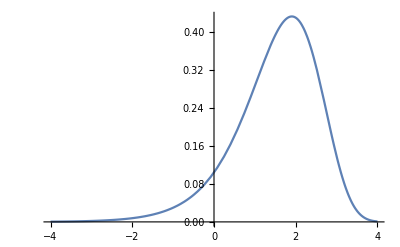

```mathematica
Plot[Σ/(√(2π))Exp[3Σ(x-μ)/2-E^(Σ(x-μ))/2],{x,-4,4}]
```

```mathematica
(*Parameters*)
y0=2-EulerGamma-Log[2];
Σ=Sqrt[(1/4) (Pi^2-8)];

(*Characteristic function of the standardized log-Mach distribution*)
phiY[t_]:=(4 Exp[EulerGamma-2])^(I t/Σ)*(2/Sqrt[Pi])*Gamma[3/2+I t/Σ];

(*Characteristic function of s=sum y_i/sqrt(n)*)
phi[n_,t_]:=(phiY[t/Sqrt[n]])^n;

(*PDF via inverse Fourier transform*)
fPDF[n_,s_]:=Re[NIntegrate[Exp[-I t s]*phi[n,t],{t,-100,100},Method->{"GlobalAdaptive","MaxErrorIncreases"->100},MaxRecursion->15,AccuracyGoal->6,PrecisionGoal->6]/(2 Pi)];

(*Range of s*)
sRange={-5,5};
sVals=Subdivide[sRange[[1]],sRange[[2]],400];

(*Values of n*)
nList={1,2,3,4,5,10,20,30,40,50,100,200,300,400,500};

(*Loop over n values and plot each individually*)
plots=Table[Module[{data},Print["Computing PDF for n = ",n];
data=Table[{s,fPDF[n,s]},{s,sVals}];
ListLinePlot[data,PlotRange->{{-4.5,4.5},{0,0.5}},PlotStyle->{Thick,Black},AxesLabel->{"s","PDF"},PlotLabel->Row[{"PDF of s for ",Style["n = "<>ToString[n],Bold]}],ImageSize->Large]],{n,nList}];
```

Computing PDF for n = 1

ListLinePlot::prng: Value of option PlotRange -> {{-4.5},{4.5},{0,0.5}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Computing PDF for n = 2

ListLinePlot::prng: Value of option PlotRange -> {{-4.5},{4.5},{0,0.5}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Computing PDF for n = 3

ListLinePlot::prng: Value of option PlotRange -> {{-4.5},{4.5},{0,0.5}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of ListLinePlot::prng will be suppressed during this calculation.

Computing PDF for n = 4

Computing PDF for n = 5

$Aborted

```mathematica
Do[Export["work/promote/CLT_plots/logrho_ideal_n"<>ToString[nList[[i]]]<>".png",plots[[i]]],{i,Length[nList]}]
```